```mathematica
pixels=26763.458;
cpuUnlock= 2901430.667;
```

```mathematica
pixelsCount=19573;
```

```mathematica
pixelsCount*pixels
```

5.23841×10^8

```mathematica
pixelsCount*pixels/cpuUnlock
```

180.546

## Energy

```mathematica
energyCr=5.3;
batteryCr=15.452;
```

```mathematica
batteryCr*50/500
```

1.5452

```mathematica
energyCr*600/50
```

63.6

## Minerals

```mathematica
costMatrix=({{"Name", "Mineral", "Mineral Bar"}, {"Utrium", 1.747, 11.552}, {"Lemergium", 12.139, 68.917}, {"Zynthium", 2.229, 32.581}, {"Keanium", 0.477, 4.807}, {"Ghodium", 16.783, 89.404}, {"Oxygen", 2.335, 22.284}, {"Hydrogen", 8.852, 44.301}, {"Catalyst", 2.309, 12.797}});
```

```mathematica
n=Length[costMatrix];
```

```mathematica
BarToRawCost=(costMatrix[[2;;,2]]*100+energyCr*200)/500;
```

```mathematica
RawToBarCost=(costMatrix[[2;;,2]]*500+energyCr*200)/100;
```

```mathematica
BarToRawProfit=costMatrix[[2;;,2]]-BarToRawCost;
BarToRawProfitPer=BarToRawProfit/costMatrix[[2;;,2]];
```

```mathematica
RawToBarProfit=costMatrix[[2;;,3]]-RawToBarCost;
RawToBarProfitPer=RawToBarProfit/costMatrix[[2;;,3]];
```

```mathematica
profitTable=Transpose[{
costMatrix[[;;,1]],
Insert[BarToRawProfit,"Bar to Raw",1],
Insert[BarToRawProfitPer*100,"BR%",1],
Insert[RawToBarProfit,"Raw to Bar",1],
Insert[RawToBarProfitPer*100,"RB%",1]
}];
profitTableClean=Transpose[{
BarToRawProfit,BarToRawProfitPer*100,
RawToBarProfit,RawToBarProfitPer*100}];
```

```mathematica
(*TableForm[profitTable,TableAlignments->{Right, Top}]*)
```

```mathematica
labels={"B-R","B-R%","R-B","R-B%"};
```

```mathematica
TableForm[profitTableClean,TableHeadings->{costMatrix[[2;;,1]],labels},TableAlignments->Center]
```

| B-R | B-R% | R-B | R-B%
Utrium | -0.7224 | -41.3509 | -7.783 | -67.3736
Lemergium | 7.5912 | 62.5356 | -2.378 | -3.45053
Zynthium | -0.3368 | -15.1099 | 10.836 | 33.2586
Keanium | -1.7384 | -364.444 | -8.178 | -170.127
Ghodium | 11.3064 | 67.3682 | -5.111 | -5.71675
Oxygen | -0.252 | -10.7923 | 0.009 | 0.0403877
Hydrogen | 4.9616 | 56.0506 | -10.559 | -23.8347
Catalyst | -0.2728 | -11.8146 | -9.348 | -73.0484

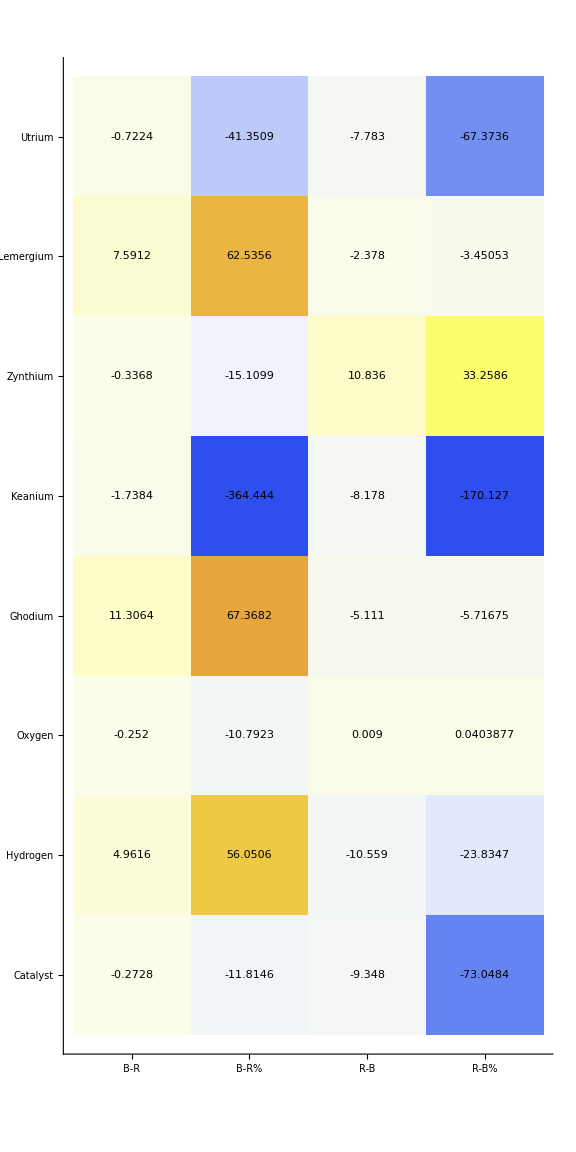

```mathematica
ArrayPlot[profitTableClean,
ColorFunction->ColorData[{"TemperatureMap",{-100,100}}],ColorFunctionScaling->False,Axes->True,Frame->False,
Ticks->{Table[{j-0.5,labels[[j]]},{j,1,4}],Table[{n-j-0.5,costMatrix[[j+1,1]]},{j,1n-1}]},ImageSize->Large,
Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[profitTableClean],{2}]}
]
```